Define everything in one place.

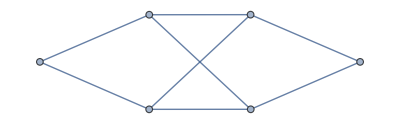

```mathematica
SetDirectory["~/Documents/UNH/Research/code/OTimes/sp4/"];
Clear[GammaAdj, GammaSymb, q, rho,n, dim, lvl, braid];
GammaAdj = { 
{0,1,1,0,0,0},
{1,0,0,1,1,0},
{1,0,0,1,1,0}, 
{0,1,1,0,0,1},
{0,1,1,0,0,1},
{0,0,0,1,1,0} 
};
AdjacencyGraph[ GammaAdj] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
GammaSymb = { 
{0,aa,bb,0,0,0},
{cc,0,0,dd,ee,0},
{ff,0,0,gg,hh,0}, 
{0,ii,jj,0,0,kk},
{0,ll,mm,0,0,nn},
{0,0,0,oo,pp,0}
};
quan[n_, qew_]:=(qew^n-qew^-n)/(qew-qew^-1);
inDeg[z_]:=360(z//Arg)/(2Pi)//N
dim=2;
lvl = 3;
q=AlgebraicNumber"0.966"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-1339947038318497824042054379340224188424396116226678218098746796796408746191132980696413338764113250280671161186017258829796639550661461533832401727/2370999073893603146083203759119869452862559369549759692155537072171686985346145191498188014223753818764622191973847070734180294896688571062539863872,«30»,-98245651314592044693777734500129325005915455945333252338214360185670145735558898777861037554864301452324901754188480255969981454903597/74093721059175098315100117472495920401954980298429990379860533505365218292067037234318375444492306836394443499182720960443134215521517845704370746}]0.9659258262890683;
oldq = Exp[(2Pi I)/(4(dim+lvl+1))];
rho = q^5; (* should this be -q^5??? *)
delta = AlgebraicNumber"-2.73"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{6576861998005468661988260352212931034879803751932280586426154747395880119014803787378868000271857/5438968486858934520291453431313375668724773103453917545882589843955893509910644819297679763969528,2189892652716070548076565602304622149250874844722065942041459786282536757686971728022854104381505/453247373904911210024287785942781305727064425287826462156882486996324459159220401608139980330794,«29»,13603222880024208194116052280686236975152976713817455696137293236618368710091091789115/1812989495619644840097151143771125222908257701151305848627529947985297836636881606432559921323176}]-2.732050807568877;

Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom2to4 = GetHomBasisList[GammaSymb, 2,4];
Hom2to3 = GetHomBasisList[GammaSymb, 2,3];
Hom2to2 = GetHomBasisList[GammaSymb,2,2];
Hom2to1 = GetHomBasisList[GammaSymb,2,1];
Hom2to0 = GetHomBasisList[GammaSymb,2,0];
Hom1to2 = GetHomBasisList[GammaSymb,1,2];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom1to0 = GetHomBasisList[GammaSymb,1,0];
Hom0to1 = GetHomBasisList[GammaSymb,0,1];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom3to3 = GetHomBasisList[GammaSymb, 3,3];
Cap = GenerateCap[GammaAdj, GammaSymb];
Cup = InTermsOf[Dagger[Cap], Hom0to2];
Cup = ScaleByConstant[Cup, -1];
Stick = GenerateStick[GammaAdj, GammaSymb];
DoubleStick = InTermsOf[BigTens[Stick, Stick], Hom2to2];

braidSol = {Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,1/2,1,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),1/4 (-1+√3),1+√3,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"-0.448"+"0.259" ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268,-√(-1+√3),-√(2 (1+√3)),-1/2 √(-1+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,√(2+√3),Root"-0.157"Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772,(√(2-√3))/2,Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,-1/(√2),-1/(√2),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),((1/2+ⅈ/2) ((-2+ⅈ)+√3))/(√2),-1/2 √(-1+√3),Root"-0.157"Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772,-√(-1+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,(√(2-√3))/2,-√(2 (1+√3)),√(2+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,(√(2-√3))/2,√(2+√3),1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),1,1/2,1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,1/4 (√2-√6),√(1/2 (-1+√3)),-√(2+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-√(1+√3),√(1/2 (-1+√3)),-1/2 √(-5+3 √3),Root"-0.448"+"0.259" ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,1+√3,1/4 (-1+√3),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-√(2+√3),√(1/2 (-1+√3)),1/4 (√2-√6),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-1/2 √(-5+3 √3),√(1/2 (-1+√3)),-√(1+√3),(ⅈ-√3)/(√2+√6),Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,-1/(√2),-1/(√2),Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),√(2+√3),(√(2-√3))/2,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738};
newBraidSol = {AlgebraicNumber"-0.354"+"0.612" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-4209993212160212780798154587040396054078649077267772752098051945143420080871321381973765483779372487228905003905083285458969473691/3077603151819911113121544211342625626537243877461901325199753379582180907630553232095371249560325021269775752915818628585129984256,«30»,-187300986120505234539879730369987364267161925951215763042367923724585960592341166911109836899566886652630588733638931/48087549247186111142524128302228525414644435585342208206246146555971576681727394251490175774380078457340246139309666071642656004}]-0.3535533905932738,AlgebraicNumber"0.612"+"0.354" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{18638779581425067965708154020697582611527423030942531496327889477683595447702259172982336855131508004213876673322966952460802209/158853939035086093664475197167310075825068648580174325856802914566874476372516713464026530390225632235231095470178740561935369472,«30»,15564350290987281349273358070084709060217753095052606241387473416094730436392759764495821378847967860924204922947997/4412609417641280379568755476869724328474129127227064607133414293524291010347686485111848066395156450978641540838298348942649152}]0.6123724356957945,AlgebraicNumber"0.612"+"0.354" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{18638779581425067965708154020697582611527423030942531496327889477683595447702259172982336855131508004213876673322966952460802209/158853939035086093664475197167310075825068648580174325856802914566874476372516713464026530390225632235231095470178740561935369472,«30»,15564350290987281349273358070084709060217753095052606241387473416094730436392759764495821378847967860924204922947997/4412609417641280379568755476869724328474129127227064607133414293524291010347686485111848066395156450978641540838298348942649152}]0.6123724356957945,AlgebraicNumber"-0.354"+"0.612" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-4209993212160212780798154587040396054078649077267772752098051945143420080871321381973765483779372487228905003905083285458969473691/3077603151819911113121544211342625626537243877461901325199753379582180907630553232095371249560325021269775752915818628585129984256,«30»,-187300986120505234539879730369987364267161925951215763042367923724585960592341166911109836899566886652630588733638931/48087549247186111142524128302228525414644435585342208206246146555971576681727394251490175774380078457340246139309666071642656004}]-0.3535533905932738,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,1/2,1,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"0.183"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-17454798971723337702571167214839682372329349958840115678191334435307667138836093425974227528210913/21755873947435738081165813725253502674899092413815670183530359375823574039642579277190719055878112,-2189892652716070548076565602304622149250874844722065942041459786282536757686971728022854104381505/1812989495619644840097151143771125222908257701151305848627529947985297836636881606432559921323176,«29»,-13603222880024208194116052280686236975152976713817455696137293236618368710091091789115/7251957982478579360388604575084500891633030804605223394510119791941191346547526425730239685292704}]0.18301270189221933,AlgebraicNumber"2.73"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-6576861998005468661988260352212931034879803751932280586426154747395880119014803787378868000271857/5438968486858934520291453431313375668724773103453917545882589843955893509910644819297679763969528,-2189892652716070548076565602304622149250874844722065942041459786282536757686971728022854104381505/453247373904911210024287785942781305727064425287826462156882486996324459159220401608139980330794,«29»,-13603222880024208194116052280686236975152976713817455696137293236618368710091091789115/1812989495619644840097151143771125222908257701151305848627529947985297836636881606432559921323176}]2.732050807568877,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,AlgebraicNumber"0.259"+"0.448" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3792678043959455952006904455166208063058876300834210222665631498067472482033224936166037402011166434387454489698810000993094523006035805089315782615/4741998147787206292166407518239738905725118739099519384311074144343373970692290382996376028447507637529244383947694141468360589793377142125079727744,«30»,9935022784964624085159321196011147532520609196158495692242166207317597903791405455479920564922266513291700529663999948491982132305279469/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936}]0.25881904510252074,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-1119581267771786671251988510692506176293902660372543004827061969350232821615551478259198931263110105519771608532442981884162814057880386683/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-548644157344035199818997577792711522750906927766682730974386465826767139646925766025249431115098428220997404626254463071805119/45176906793689336420183441310963751823577475201013665268698809060223381739150598955990768179742644776016066415436423131501836776112199616}]0.48171652200114257,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"-0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-547786927051660172608366092410342015946351674944234392600333756717349816705228077057448998184163784004026142182302022000589279155395022779/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-725369465170531362406556180464554920958965445366989329136332740945964322865933213510624468799998283613657007112535444326324765/135530720381068009260550323932891255470732425603040995806096427180670145217451796867972304539227934328048199246309269394505510328336598848}]-0.48171652200114257,AlgebraicNumber"-0.448"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3031116991966893960551037234115749991097578941278440878929183576919659065376642681536507705754444467738845807766047500804168928400052320506642281545/2370999073893603146083203759119869452862559369549759692155537072171686985346145191498188014223753818764622191973847070734180294896688571062539863872,«30»,-587415289659078593468219757069869436171182431062463468742908643786239598924155580573948587165173837255497137738136762934617773274591401/1580666049262402097388802506079912968575039579699839794770358048114457990230763460998792009482502545843081461315898047156120196597792380708359909248}]-0.4482877360840268,AlgebraicNumber"-0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3114357292236341205718434671732902899898911812074190599738999190493446958432753302213964957895629236861539949972937265284428958301/8705300334595933848407260571263753263829367515595279921083909038846189563031610182035188627613169193364588238683653825031229678336,«30»,-1724423356434635329426978384141652558790027584398449269227469232781492153213577454439726701350054840379721347694208089/1450883389099322308067876761877292210638227919265879986847318173141031593838601697005864771268861532227431373113942304171871613056}]-0.8555996771673522,AlgebraicNumber"-2.34"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{24299716601979220118518052233144652604860281699048969191638564882199895245066136754862364402009027985753117399992437086927199111661/8705300334595933848407260571263753263829367515595279921083909038846189563031610182035188627613169193364588238683653825031229678336,«30»,12563603950988010279754810874638513788966990828225113626158828560758917671745154168258070073554611283049300600091802521/2901766778198644616135753523754584421276455838531759973694636346282063187677203394011729542537723064454862746227884608343743226112}]-2.3375417889607353,AlgebraicNumber"-0.428"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3114357292236341205718434671732902899898911812074190599738999190493446958432753302213964957895629236861539949972937265284428958301/17410600669191867696814521142527506527658735031190559842167818077692379126063220364070377255226338386729176477367307650062459356672,«30»,-1724423356434635329426978384141652558790027584398449269227469232781492153213577454439726701350054840379721347694208089/2901766778198644616135753523754584421276455838531759973694636346282063187677203394011729542537723064454862746227884608343743226112}]-0.4277998385836761,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"1.93"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{26187455773277866345274587489371135446030439215138323226890306366758725304997303947512052565567685046360391046554967649102915488171/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888,«30»,173502278043659601331644973387085597417573070854983052568377549246141750665077328571671088996441403437144363991176072909/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888}]1.9318516525781366,AlgebraicNumber"-0.157"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{18071002017506537707081182889678846805062458074900587992160566501213001328200630150434434486217769512030037500046562556358341195059/34821201338383735393629042285055013055317470062381119684335636155384758252126440728140754510452676773458352954734615300124918713344,«30»,19461297376726551597462724411205124024127101165818910703068705491884886284599463986016976878954830644568185990868634877/11607067112794578464543014095018337685105823354127039894778545385128252750708813576046918170150892257819450984911538433374972904448}]-0.15658560865650772,AlgebraicNumber"0.259"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{78655651045500751538990269313211831543373437336833804824880601458679239521225617774716845003645778769099384858668536335274868036659/56920713829573819241528787952545332599829102216024070730167612773008326068231333036881988832988268085553902716702576066699063131776,«30»,401326237747484326323183790437602432514614082960550052780080727837122252976583438932982087289027664324281883040849526463/113841427659147638483057575905090665199658204432048141460335225546016652136462666073763977665976536171107805433405152133398126263552}]0.25881904510252074,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"-0.707"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{591614233067828811837166798443775489843471654419668499088572498865262385129868594021/641819378067775140818073184998180805685875587212853544149039036929078124252981733392,204519032314607611711961460988547264571979212108154270318772712382695884961706986203/1711518341514067042181528493328482148495668232567609451064104098477541664674617955712,«28»,68444074407442593357920767574522779798850465125059476619532897097313451/933555459007672932099015541815535717361273581400514246034965871896840908004337066752,4900108321636469983646605463110817941320472981979616496755914058163270345/10269110049084402253089170959970892890974009395405656706384624590865249988047707734272}]-0.7071067811865476,AlgebraicNumber"-0.707"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{591614233067828811837166798443775489843471654419668499088572498865262385129868594021/641819378067775140818073184998180805685875587212853544149039036929078124252981733392,204519032314607611711961460988547264571979212108154270318772712382695884961706986203/1711518341514067042181528493328482148495668232567609451064104098477541664674617955712,«28»,68444074407442593357920767574522779798850465125059476619532897097313451/933555459007672932099015541815535717361273581400514246034965871896840908004337066752,4900108321636469983646605463110817941320472981979616496755914058163270345/10269110049084402253089170959970892890974009395405656706384624590865249988047707734272}]-0.7071067811865476,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,AlgebraicNumber"-0.448"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3031116991966893960551037234115749991097578941278440878929183576919659065376642681536507705754444467738845807766047500804168928400052320506642281545/2370999073893603146083203759119869452862559369549759692155537072171686985346145191498188014223753818764622191973847070734180294896688571062539863872,«30»,-587415289659078593468219757069869436171182431062463468742908643786239598924155580573948587165173837255497137738136762934617773274591401/1580666049262402097388802506079912968575039579699839794770358048114457990230763460998792009482502545843081461315898047156120196597792380708359909248}]-0.4482877360840268,AlgebraicNumber"-0.428"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3114357292236341205718434671732902899898911812074190599738999190493446958432753302213964957895629236861539949972937265284428958301/17410600669191867696814521142527506527658735031190559842167818077692379126063220364070377255226338386729176477367307650062459356672,«30»,-1724423356434635329426978384141652558790027584398449269227469232781492153213577454439726701350054840379721347694208089/2901766778198644616135753523754584421276455838531759973694636346282063187677203394011729542537723064454862746227884608343743226112}]-0.4277998385836761,AlgebraicNumber"-0.157"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{18071002017506537707081182889678846805062458074900587992160566501213001328200630150434434486217769512030037500046562556358341195059/34821201338383735393629042285055013055317470062381119684335636155384758252126440728140754510452676773458352954734615300124918713344,«30»,19461297376726551597462724411205124024127101165818910703068705491884886284599463986016976878954830644568185990868634877/11607067112794578464543014095018337685105823354127039894778545385128252750708813576046918170150892257819450984911538433374972904448}]-0.15658560865650772,AlgebraicNumber"-0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3114357292236341205718434671732902899898911812074190599738999190493446958432753302213964957895629236861539949972937265284428958301/8705300334595933848407260571263753263829367515595279921083909038846189563031610182035188627613169193364588238683653825031229678336,«30»,-1724423356434635329426978384141652558790027584398449269227469232781492153213577454439726701350054840379721347694208089/1450883389099322308067876761877292210638227919265879986847318173141031593838601697005864771268861532227431373113942304171871613056}]-0.8555996771673522,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"0.259"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{78655651045500751538990269313211831543373437336833804824880601458679239521225617774716845003645778769099384858668536335274868036659/56920713829573819241528787952545332599829102216024070730167612773008326068231333036881988832988268085553902716702576066699063131776,«30»,401326237747484326323183790437602432514614082960550052780080727837122252976583438932982087289027664324281883040849526463/113841427659147638483057575905090665199658204432048141460335225546016652136462666073763977665976536171107805433405152133398126263552}]0.25881904510252074,AlgebraicNumber"-2.34"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{24299716601979220118518052233144652604860281699048969191638564882199895245066136754862364402009027985753117399992437086927199111661/8705300334595933848407260571263753263829367515595279921083909038846189563031610182035188627613169193364588238683653825031229678336,«30»,12563603950988010279754810874638513788966990828225113626158828560758917671745154168258070073554611283049300600091802521/2901766778198644616135753523754584421276455838531759973694636346282063187677203394011729542537723064454862746227884608343743226112}]-2.3375417889607353,AlgebraicNumber"1.93"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{26187455773277866345274587489371135446030439215138323226890306366758725304997303947512052565567685046360391046554967649102915488171/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888,«30»,173502278043659601331644973387085597417573070854983052568377549246141750665077328571671088996441403437144363991176072909/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888}]1.9318516525781366,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"0.259"+"0.448" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3792678043959455952006904455166208063058876300834210222665631498067472482033224936166037402011166434387454489698810000993094523006035805089315782615/4741998147787206292166407518239738905725118739099519384311074144343373970692290382996376028447507637529244383947694141468360589793377142125079727744,«30»,9935022784964624085159321196011147532520609196158495692242166207317597903791405455479920564922266513291700529663999948491982132305279469/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936}]0.25881904510252074,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"-0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-547786927051660172608366092410342015946351674944234392600333756717349816705228077057448998184163784004026142182302022000589279155395022779/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-725369465170531362406556180464554920958965445366989329136332740945964322865933213510624468799998283613657007112535444326324765/135530720381068009260550323932891255470732425603040995806096427180670145217451796867972304539227934328048199246309269394505510328336598848}]-0.48171652200114257,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-1119581267771786671251988510692506176293902660372543004827061969350232821615551478259198931263110105519771608532442981884162814057880386683/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-548644157344035199818997577792711522750906927766682730974386465826767139646925766025249431115098428220997404626254463071805119/45176906793689336420183441310963751823577475201013665268698809060223381739150598955990768179742644776016066415436423131501836776112199616}]0.48171652200114257,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,AlgebraicNumber"0.259"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{78655651045500751538990269313211831543373437336833804824880601458679239521225617774716845003645778769099384858668536335274868036659/56920713829573819241528787952545332599829102216024070730167612773008326068231333036881988832988268085553902716702576066699063131776,«30»,401326237747484326323183790437602432514614082960550052780080727837122252976583438932982087289027664324281883040849526463/113841427659147638483057575905090665199658204432048141460335225546016652136462666073763977665976536171107805433405152133398126263552}]0.25881904510252074,AlgebraicNumber"1.93"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{26187455773277866345274587489371135446030439215138323226890306366758725304997303947512052565567685046360391046554967649102915488171/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888,«30»,173502278043659601331644973387085597417573070854983052568377549246141750665077328571671088996441403437144363991176072909/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888}]1.9318516525781366,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,1,1/2,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"-0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-547786927051660172608366092410342015946351674944234392600333756717349816705228077057448998184163784004026142182302022000589279155395022779/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-725369465170531362406556180464554920958965445366989329136332740945964322865933213510624468799998283613657007112535444326324765/135530720381068009260550323932891255470732425603040995806096427180670145217451796867972304539227934328048199246309269394505510328336598848}]-0.48171652200114257,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-1119581267771786671251988510692506176293902660372543004827061969350232821615551478259198931263110105519771608532442981884162814057880386683/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-548644157344035199818997577792711522750906927766682730974386465826767139646925766025249431115098428220997404626254463071805119/45176906793689336420183441310963751823577475201013665268698809060223381739150598955990768179742644776016066415436423131501836776112199616}]0.48171652200114257,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.259"+"0.448" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3792678043959455952006904455166208063058876300834210222665631498067472482033224936166037402011166434387454489698810000993094523006035805089315782615/4741998147787206292166407518239738905725118739099519384311074144343373970692290382996376028447507637529244383947694141468360589793377142125079727744,«30»,9935022784964624085159321196011147532520609196158495692242166207317597903791405455479920564922266513291700529663999948491982132305279469/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936}]0.25881904510252074,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"-0.259"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-78655651045500751538990269313211831543373437336833804824880601458679239521225617774716845003645778769099384858668536335274868036659/56920713829573819241528787952545332599829102216024070730167612773008326068231333036881988832988268085553902716702576066699063131776,«30»,-401326237747484326323183790437602432514614082960550052780080727837122252976583438932982087289027664324281883040849526463/113841427659147638483057575905090665199658204432048141460335225546016652136462666073763977665976536171107805433405152133398126263552}]-0.25881904510252074,AlgebraicNumber"0.605"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-16969277557203500747054024633532902981040802502575709294590185015883797270509615246708122758130903896430231811706701388521896243/71797370921685831443394050069647440298169391685639882656277322138725401653940043387524129590689735832460476001910923766883501568,«30»,-1930180647845070240779746638730297119909097968312814694448599391484737917558350581657238664503458495768371314241207/725225968905917489327212626966135760587569612986261440972498203421468703575151953409334642330199351843035111130413371382661632}]0.6050003337060557,AlgebraicNumber"-1.93"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-26187455773277866345274587489371135446030439215138323226890306366758725304997303947512052565567685046360391046554967649102915488171/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888,«30»,-173502278043659601331644973387085597417573070854983052568377549246141750665077328571671088996441403437144363991176072909/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888}]-1.9318516525781366,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"-1.65"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-86621647670449446831075050056144877542978686867528010386990634840575909484198644671030437037083868994836426909633276758167990109/35898685460842915721697025034823720149084695842819941328138661069362700826970021693762064795344867916230238000955461883441750784,«30»,-4365465636117182780813660359230296492681877470494312937502587460891591946042619275000651099191594888299480776339183/1087838953358876233990818940449203640881354419479392161458747305132203055362727930114001963495299027764552666695620057073992448}]-1.6528916502810695,AlgebraicNumber"0.605"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-16969277557203500747054024633532902981040802502575709294590185015883797270509615246708122758130903896430231811706701388521896243/71797370921685831443394050069647440298169391685639882656277322138725401653940043387524129590689735832460476001910923766883501568,«30»,-1930180647845070240779746638730297119909097968312814694448599391484737917558350581657238664503458495768371314241207/725225968905917489327212626966135760587569612986261440972498203421468703575151953409334642330199351843035111130413371382661632}]0.6050003337060557,AlgebraicNumber"-0.221"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-6474432826728309223633067168104861282751218085631482480098801241028731672169266244858659987200923305704166170083748634168117897/4487335682605364465212128129352965018635586980352492666017332633670337603371252711720258099418108489528779750119432735430218848,«30»,-2539001894913098375788225068855296963102292843858189255212096408836451424679417754993091773175492593901148679765701/543919476679438116995409470224601820440677209739696080729373652566101527681363965057000981747649513882276333347810028536996224}]-0.22144549143447914,AlgebraicNumber"-0.448"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3031116991966893960551037234115749991097578941278440878929183576919659065376642681536507705754444467738845807766047500804168928400052320506642281545/2370999073893603146083203759119869452862559369549759692155537072171686985346145191498188014223753818764622191973847070734180294896688571062539863872,«30»,-587415289659078593468219757069869436171182431062463468742908643786239598924155580573948587165173837255497137738136762934617773274591401/1580666049262402097388802506079912968575039579699839794770358048114457990230763460998792009482502545843081461315898047156120196597792380708359909248}]-0.4482877360840268,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"2.73"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-6576861998005468661988260352212931034879803751932280586426154747395880119014803787378868000271857/5438968486858934520291453431313375668724773103453917545882589843955893509910644819297679763969528,-2189892652716070548076565602304622149250874844722065942041459786282536757686971728022854104381505/453247373904911210024287785942781305727064425287826462156882486996324459159220401608139980330794,«29»,-13603222880024208194116052280686236975152976713817455696137293236618368710091091789115/1812989495619644840097151143771125222908257701151305848627529947985297836636881606432559921323176}]2.732050807568877,AlgebraicNumber"0.183"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-17454798971723337702571167214839682372329349958840115678191334435307667138836093425974227528210913/21755873947435738081165813725253502674899092413815670183530359375823574039642579277190719055878112,-2189892652716070548076565602304622149250874844722065942041459786282536757686971728022854104381505/1812989495619644840097151143771125222908257701151305848627529947985297836636881606432559921323176,«29»,-13603222880024208194116052280686236975152976713817455696137293236618368710091091789115/7251957982478579360388604575084500891633030804605223394510119791941191346547526425730239685292704}]0.18301270189221933,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"-1.93"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-26187455773277866345274587489371135446030439215138323226890306366758725304997303947512052565567685046360391046554967649102915488171/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888,«30»,-173502278043659601331644973387085597417573070854983052568377549246141750665077328571671088996441403437144363991176072909/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888}]-1.9318516525781366,AlgebraicNumber"0.605"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-16969277557203500747054024633532902981040802502575709294590185015883797270509615246708122758130903896430231811706701388521896243/71797370921685831443394050069647440298169391685639882656277322138725401653940043387524129590689735832460476001910923766883501568,«30»,-1930180647845070240779746638730297119909097968312814694448599391484737917558350581657238664503458495768371314241207/725225968905917489327212626966135760587569612986261440972498203421468703575151953409334642330199351843035111130413371382661632}]0.6050003337060557,AlgebraicNumber"-0.259"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-78655651045500751538990269313211831543373437336833804824880601458679239521225617774716845003645778769099384858668536335274868036659/56920713829573819241528787952545332599829102216024070730167612773008326068231333036881988832988268085553902716702576066699063131776,«30»,-401326237747484326323183790437602432514614082960550052780080727837122252976583438932982087289027664324281883040849526463/113841427659147638483057575905090665199658204432048141460335225546016652136462666073763977665976536171107805433405152133398126263552}]-0.25881904510252074,AlgebraicNumber"-0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-2853562694760012978161914575587183954752116350400649017200850986981438361573229014291854914041403525908694448732743298178081798241224588291467439431/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936,«30»,-74918007253210847081744127916406914605543347743706482303518765713947710080583974077415541904443362252751798361461404335479539402736496505/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]-0.25881904510252074,AlgebraicNumber"-0.221"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-6474432826728309223633067168104861282751218085631482480098801241028731672169266244858659987200923305704166170083748634168117897/4487335682605364465212128129352965018635586980352492666017332633670337603371252711720258099418108489528779750119432735430218848,«30»,-2539001894913098375788225068855296963102292843858189255212096408836451424679417754993091773175492593901148679765701/543919476679438116995409470224601820440677209739696080729373652566101527681363965057000981747649513882276333347810028536996224}]-0.22144549143447914,AlgebraicNumber"0.605"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-16969277557203500747054024633532902981040802502575709294590185015883797270509615246708122758130903896430231811706701388521896243/71797370921685831443394050069647440298169391685639882656277322138725401653940043387524129590689735832460476001910923766883501568,«30»,-1930180647845070240779746638730297119909097968312814694448599391484737917558350581657238664503458495768371314241207/725225968905917489327212626966135760587569612986261440972498203421468703575151953409334642330199351843035111130413371382661632}]0.6050003337060557,AlgebraicNumber"-1.65"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-86621647670449446831075050056144877542978686867528010386990634840575909484198644671030437037083868994836426909633276758167990109/35898685460842915721697025034823720149084695842819941328138661069362700826970021693762064795344867916230238000955461883441750784,«30»,-4365465636117182780813660359230296492681877470494312937502587460891591946042619275000651099191594888299480776339183/1087838953358876233990818940449203640881354419479392161458747305132203055362727930114001963495299027764552666695620057073992448}]-1.6528916502810695,AlgebraicNumber"-0.448"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3031116991966893960551037234115749991097578941278440878929183576919659065376642681536507705754444467738845807766047500804168928400052320506642281545/2370999073893603146083203759119869452862559369549759692155537072171686985346145191498188014223753818764622191973847070734180294896688571062539863872,«30»,-587415289659078593468219757069869436171182431062463468742908643786239598924155580573948587165173837255497137738136762934617773274591401/1580666049262402097388802506079912968575039579699839794770358048114457990230763460998792009482502545843081461315898047156120196597792380708359909248}]-0.4482877360840268,AlgebraicNumber"0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-1119581267771786671251988510692506176293902660372543004827061969350232821615551478259198931263110105519771608532442981884162814057880386683/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-548644157344035199818997577792711522750906927766682730974386465826767139646925766025249431115098428220997404626254463071805119/45176906793689336420183441310963751823577475201013665268698809060223381739150598955990768179742644776016066415436423131501836776112199616}]0.48171652200114257,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.259"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{93953886313799785361610158598640322370732379169542370046135376673513906621417205602227464832796178747676369254446124554131793824966158831822771101/263444341543733682898133751013318828095839929949973299128393008019076331705127243499798668247083757640513576885983007859353366099632063451393318208,«30»,-8049967553111126640806434279217885108892136473688718555874444983241608123848236263504952165006836804715285125482473025185932132937604411/9483996295574412584332815036479477811450237478199038768622148288686747941384580765992752056895015275058488767895388282936721179586754284250159455488}]0.25881904510252074,AlgebraicNumber"-0.482"+"0.518" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-547786927051660172608366092410342015946351674944234392600333756717349816705228077057448998184163784004026142182302022000589279155395022779/406592161143204027781650971798673766412197276809122987418289281542010435652355390603916913617683802984144597738927808183516530985009796544,«30»,-725369465170531362406556180464554920958965445366989329136332740945964322865933213510624468799998283613657007112535444326324765/135530720381068009260550323932891255470732425603040995806096427180670145217451796867972304539227934328048199246309269394505510328336598848}]-0.48171652200114257,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"-0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{12072333420459704131847420687407968900032557619641746372633290770515227599495212664923497598332978332020230957988077530210828376496493405264850618155/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,1083179697309273250597953129963096193338232373784689543185390579526654059704249441235911824064714026654119376389689772405227582907848089/68115499066625518255446562762001139538227561350145908026473253295885873050897814181182663000315665942504427275532281371947722408401199779914042544}]-0.5630162503052472,AlgebraicNumber"0.563"+"0.221" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{4953049186916660350735021949288252257159334572407155992325021270692041277598806474539254611877607809539668307424320017877229711129984876000025146035/2179695970132016584174290008384036465223281963204669056847144105468347937628730053797845216010101310160141672817033003902327117068838392957249361408,«30»,10362451393967309458833323765914054137413736320707073276517963456687322692197260361059287157061030385377194581526675063877123204094423155/1089847985066008292087145004192018232611640981602334528423572052734173968814365026898922608005050655080070836408516501951163558534419196478624680704}]0.5630162503052472,AlgebraicNumber"0.259"+"0.448" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{3792678043959455952006904455166208063058876300834210222665631498067472482033224936166037402011166434387454489698810000993094523006035805089315782615/4741998147787206292166407518239738905725118739099519384311074144343373970692290382996376028447507637529244383947694141468360589793377142125079727744,«30»,9935022784964624085159321196011147532520609196158495692242166207317597903791405455479920564922266513291700529663999948491982132305279469/1185499536946801573041601879559934726431279684774879846077768536085843492673072595749094007111876909382311095986923535367090147448344285531269931936}]0.25881904510252074,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"-0.707"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{591614233067828811837166798443775489843471654419668499088572498865262385129868594021/641819378067775140818073184998180805685875587212853544149039036929078124252981733392,204519032314607611711961460988547264571979212108154270318772712382695884961706986203/1711518341514067042181528493328482148495668232567609451064104098477541664674617955712,«28»,68444074407442593357920767574522779798850465125059476619532897097313451/933555459007672932099015541815535717361273581400514246034965871896840908004337066752,4900108321636469983646605463110817941320472981979616496755914058163270345/10269110049084402253089170959970892890974009395405656706384624590865249988047707734272}]-0.7071067811865476,AlgebraicNumber"-0.707"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{591614233067828811837166798443775489843471654419668499088572498865262385129868594021/641819378067775140818073184998180805685875587212853544149039036929078124252981733392,204519032314607611711961460988547264571979212108154270318772712382695884961706986203/1711518341514067042181528493328482148495668232567609451064104098477541664674617955712,«28»,68444074407442593357920767574522779798850465125059476619532897097313451/933555459007672932099015541815535717361273581400514246034965871896840908004337066752,4900108321636469983646605463110817941320472981979616496755914058163270345/10269110049084402253089170959970892890974009395405656706384624590865249988047707734272}]-0.7071067811865476,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,AlgebraicNumber"0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3331555609672662679103916656006467627993009844202488922055708025333832979033116240998042356809512247186041263400667423123545309643213982043/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-455356569860111347719219601306679335179562311779031162585552659554657147939036614654713741856578412414949471354791711557811159/90353813587378672840366882621927503647154950402027330537397618120446763478301197911981536359485289552032132830872846263003673552224399232}]0.6580370064762462,AlgebraicNumber"1.93"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{26187455773277866345274587489371135446030439215138323226890306366758725304997303947512052565567685046360391046554967649102915488171/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888,«30»,173502278043659601331644973387085597417573070854983052568377549246141750665077328571671088996441403437144363991176072909/28460356914786909620764393976272666299914551108012035365083806386504163034115666518440994416494134042776951358351288033349531565888}]1.9318516525781366,AlgebraicNumber"0.259"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{78655651045500751538990269313211831543373437336833804824880601458679239521225617774716845003645778769099384858668536335274868036659/56920713829573819241528787952545332599829102216024070730167612773008326068231333036881988832988268085553902716702576066699063131776,«30»,401326237747484326323183790437602432514614082960550052780080727837122252976583438932982087289027664324281883040849526463/113841427659147638483057575905090665199658204432048141460335225546016652136462666073763977665976536171107805433405152133398126263552}]0.25881904510252074,AlgebraicNumber"-0.658"+"0.259" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-3337917169621124696337501756404925140968007497064620667653874878936497574250001980268549360979583310909149739458312592415463063209887655805/3252737289145632222253207774389390131297578214472983899346314252336083485218843124831335308941470423873156781911422465468132247880078372352,«30»,-1005232227622302918705890109922651483672999293329944034302834159762294297989600667622231536575558331031800806926923698868306645/271061440762136018521100647865782510941464851206081991612192854361340290434903593735944609078455868656096398492618538789011020656673197696}]-0.6580370064762462,AlgebraicNumber"-0.354"+"0.612" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-4209993212160212780798154587040396054078649077267772752098051945143420080871321381973765483779372487228905003905083285458969473691/3077603151819911113121544211342625626537243877461901325199753379582180907630553232095371249560325021269775752915818628585129984256,«30»,-187300986120505234539879730369987364267161925951215763042367923724585960592341166911109836899566886652630588733638931/48087549247186111142524128302228525414644435585342208206246146555971576681727394251490175774380078457340246139309666071642656004}]-0.3535533905932738,AlgebraicNumber"0.612"+"0.354" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{18638779581425067965708154020697582611527423030942531496327889477683595447702259172982336855131508004213876673322966952460802209/158853939035086093664475197167310075825068648580174325856802914566874476372516713464026530390225632235231095470178740561935369472,«30»,15564350290987281349273358070084709060217753095052606241387473416094730436392759764495821378847967860924204922947997/4412609417641280379568755476869724328474129127227064607133414293524291010347686485111848066395156450978641540838298348942649152}]0.6123724356957945,AlgebraicNumber"0.612"+"0.354" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{18638779581425067965708154020697582611527423030942531496327889477683595447702259172982336855131508004213876673322966952460802209/158853939035086093664475197167310075825068648580174325856802914566874476372516713464026530390225632235231095470178740561935369472,«30»,15564350290987281349273358070084709060217753095052606241387473416094730436392759764495821378847967860924204922947997/4412609417641280379568755476869724328474129127227064607133414293524291010347686485111848066395156450978641540838298348942649152}]0.6123724356957945,AlgebraicNumber"-0.354"+"0.612" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-4209993212160212780798154587040396054078649077267772752098051945143420080871321381973765483779372487228905003905083285458969473691/3077603151819911113121544211342625626537243877461901325199753379582180907630553232095371249560325021269775752915818628585129984256,«30»,-187300986120505234539879730369987364267161925951215763042367923724585960592341166911109836899566886652630588733638931/48087549247186111142524128302228525414644435585342208206246146555971576681727394251490175774380078457340246139309666071642656004}]-0.3535533905932738};
braid = Hom2to2;
For[i=1,i<=Length[Hom2to2],i++,
braid[[i]][["scalar"]] = newBraidSol[[i]]
];
```

```mathematica
Cap = {<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->aa**cc,"q"->1,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->bb**ff,"q"->1,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->cc**aa,"q"->2,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->dd**ii,"q"->2,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->ee**ll,"q"->2,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->ff**bb,"q"->3,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->gg**jj,"q"->3,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->hh**mm,"q"->3,"s"->3,"t"->3|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->ii**dd,"q"->4,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->jj**gg,"q"->4,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->kk**oo,"q"->4,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->ll**ee,"q"->5,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->mm**hh,"q"->5,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->nn**pp,"q"->5,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->oo**kk,"q"->6,"s"->6,"t"->6|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->pp**nn,"q"->6,"s"->6,"t"->6|>};
Cup = {<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->1,"q"->aa**cc,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->1,"q"->bb**ff,"s"->1,"t"->1|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->2,"q"->cc**aa,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->2,"q"->dd**ii,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->2,"q"->ee**ll,"s"->2,"t"->2|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->3,"q"->ff**bb,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->3,"q"->gg**jj,"s"->3,"t"->3|>,<|"scalar"->AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->3,"q"->hh**mm,"s"->3,"t"->3|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->4,"q"->ii**dd,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->4,"q"->jj**gg,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->4,"q"->kk**oo,"s"->4,"t"->4|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->5,"q"->ll**ee,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0.,"p"->5,"q"->mm**hh,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"1.00" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{355542567602120860439373169349527222319396043840789973120864350544077807672663251/200178345707678998496003476908336610633670621463621926801316877702416662609743656,«30»,(458299541165«43»0306386852213)/(181980314279«55»8787509976696)}]0. AlgebraicNumber"0.856"AlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(3114357292236341205718434671732902899898911812074190«26»3302213964957895629236861539949972937265284428958301)/(8705300334595933848407260571263753263829367515595279«26»0182035188627613169193364588238683653825031229678336),«30»,«1»}]0.8555996771673522,"p"->5,"q"->nn**pp,"s"->5,"t"->5|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->6,"q"->oo**kk,"s"->6,"t"->6|>,<|"scalar"->-AlgebraicNumber"-1.17" ⅈAlgebraicNumber[Root[831482514721+1433469169360 #1+441334787664 #1^2-1207493736576 #1^3-856822102404 #1^4+824976381760 #1^5+1092589232752 #1^6-42180637312 #1^7-670948983030 #1^8-275717747888 #1^9+223787059616 #1^10+203707004480 #1^11-31397617488 #1^12-78168215376 #1^13-4797379888 #1^14+19261371648 #1^15+3367754003 #1^16-3203032560 #1^17-801273376 #1^18+359906752 #1^19+112278128 #1^20-25974672 #1^21-9801200 #1^22+1053184 #1^23+506922 #1^24-16192 #1^25-13808 #1^26+448 #1^27+508 #1^28-16 #1^29-32 #1^30+#1^32&,32],{-(5717582409110893771522745212245182380863912291095614«15»2567072406729317028232931567078406403429835542244713)/(2114507738268482076392444983065906209834063797734674«16»4892361691155689493392772269501120688877607323100672),«30»,«1»}]0.,"p"->6,"q"->pp**nn,"s"->6,"t"->6|>};
```